Note: requires DSDdiagramV1.wl to be loaded.

```mathematica
SetDirectory[NotebookDirectory[]];
```

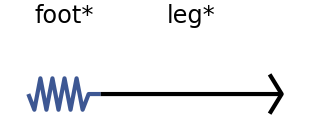

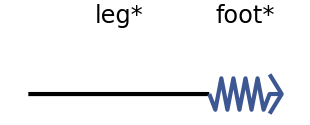

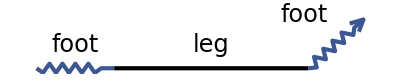

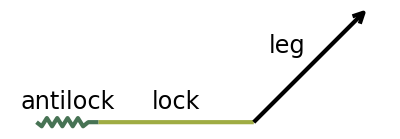

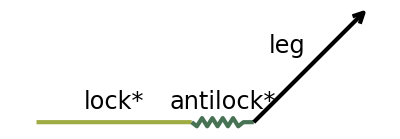

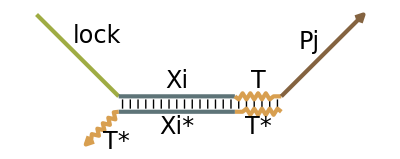

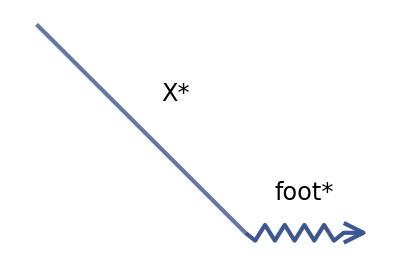

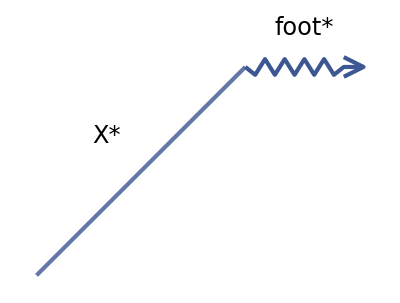

```mathematica
foot="CTCCTC";
leg="CTTCTACTTCATAAC";
antilock="ACACAC";
lock="CATTTCAACTAAACC";
T="AGTGGA";
Xi="ATGCGATTACGATCA";
Pj="GCATCTAGCTAGCTA";
X="TACGATCGATCGTAG";
cl["foot"]=1;
cl["leg"]=-1;
cl["antilock"]=2;
cl["lock"]=3;
cl["T"]=4;
cl["Xi"]=5;
cl["Pj"]=6;
cl["X"]=7;
tether1="foot* leg*";
tether2="leg* foot*";
key="foot leg @45 foot";
antilockstrand="antilock lock @45 leg";
lockstrand="lock* antilock* @45 leg";
circuit="@-45 lock @45 Xi( T( @45 Pj + ) ) @45 T*";
clasp1="@-45 X* @45 foot*";
clasp2="@45 X* @-45 foot*";
key2="@90 foot @-90 leg @-90 foot";
activator="foot X";
clasp3="X* foot*";
diagramDSD[tether1,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[tether2,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[key,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[antilockstrand,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[lockstrand,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[circuit,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[clasp1,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[clasp2,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[key2,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[activator,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
diagramDSD[clasp3,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
```

```mathematica
(* assign domain sequences *)
T1="CTCCTC";
T2="ACACAC";
X="CTTCTACTTCATAAC";
RA="CATTTCAACTAAACC";
A="CATCTCATTCTAAAC";
B="CTTACATTTCAACAC";
```

```mathematica
(* assign domain colors *)
cl["X"]=-1;
cl["RA"]=3;
cl["A"]=5;
cl["B"]=4;
```

```mathematica
(* define strands and complexes *)
gateRAtoB="@90 RA( + ) @90 X*( + B ) @90 T2*";
```

```mathematica
diagramDSD[gateRAtoB,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
```

-Graphics-